```mathematica
a={2.354978355,
1.903010033,
1.585427136,
1.485915493,
1.556985294,
1.76801406,
1.766244057,
1.51591063,
1.314639906,
1.095924453,
0.969044415,
0.974988834,
0.991917378,
0.977324263,
0.893055556,
0.767292716,
0.751923947,
0.752204176,
0.894245723,
1.093731343,
1.044551475,
0.953732264,
0.768695652,
0.630458515,
0.617867435,
0.725743855,
0.892156863,
1.037229437,
1.044776119,
0.86631016,
0.787827557,
0.732888147,
0.764285714,
0.926954733,
0.901287554,
0.861047836,
0.781542056,
0.694783574,
0.716666667,
0.829365079,
0.944693572,
0.854632588,
0.6910299,
0.555023923,
0.53164557,
0.66728972,
0.975961538,
1.140804598,
1.083333333,
0.913165266,
0.642857143,
0.644836272,
0.697802198,
0.800613497,
1.084291188,
1.06640625,
0.92519685,
0.835249042,
0.745583039,
0.813186813,
1,
1.004587156,
0.990521327,
0.743243243,
0.629787234,
0.684931507,
0.722488038,
0.915151515,
0.952702703,
0.966666667,
0.801324503,
0.794701987,
0.865248227,
0.710344828,
0.909090909,
0.916666667,
0.819672131,
0.990291262,
0.781818182,
0.763636364,
0.82,
0.892156863,
1.139534884,
1.023809524,
1.024390244,
0.692307692,
0.653061224,
0.825581395,
0.880952381,
1.317460317,
1.203125,
0.957746479,
0.810810811,
0.626506024,
0.649350649,
0.867647059,
1.083333333,
1.326923077,
1.16
}
```

{2.35498,1.90301,1.58543,1.48592,1.55699,1.76801,1.76624,1.51591,1.31464,1.09592,0.969044,0.974989,0.991917,0.977324,0.893056,0.767293,0.751924,0.752204,0.894246,1.09373,1.04455,0.953732,0.768696,0.630459,0.617867,0.725744,0.892157,1.03723,1.04478,0.86631,0.787828,0.732888,0.764286,0.926955,0.901288,0.861048,0.781542,0.694784,0.716667,0.829365,0.944694,0.854633,0.69103,0.555024,0.531646,0.66729,0.975962,1.1408,1.08333,0.913165,0.642857,0.644836,0.697802,0.800613,1.08429,1.06641,0.925197,0.835249,0.745583,0.813187,1,1.00459,0.990521,0.743243,0.629787,0.684932,0.722488,0.915152,0.952703,0.966667,0.801325,0.794702,0.865248,0.710345,0.909091,0.916667,0.819672,0.990291,0.781818,0.763636,0.82,0.892157,1.13953,1.02381,1.02439,0.692308,0.653061,0.825581,0.880952,1.31746,1.20313,0.957746,0.810811,0.626506,0.649351,0.867647,1.08333,1.32692,1.16}

```mathematica
{2,354978355.903010033.585427136.485915493.556985294.76801406.766244057.51591063.314639906.0.0.0.0.0.0.0.0.0.894245723.93731343.0.0.0.0.0.0.892156863.37229437.0.0.0.0.0.0.0.0.0.0.0.0.0.0.0.0.0.0.975961538.140804598.0.0.0.0.0.800613497.84291188.0.0.0.0.813186813.0.0.0.0.0.0.0.0.0.0.0.0.0.0.0.0.0.0.0.0.892156863.139534884.23809524.0.0.0.0.880952381.317460317.0.0.0.0.0.867647059.83333333.326923077.16}
```

```mathematica
MovingAverage[a,7]
```

{1.77437,1.6545,1.57045,1.50052,1.42668,1.34354,1.23267,1.11996,1.03098,0.952793,0.90365,0.872672,0.861138,0.875683,0.885286,0.893955,0.894155,0.876803,0.857612,0.83354,0.804744,0.803698,0.816704,0.830649,0.85313,0.869562,0.875068,0.880039,0.860619,0.834372,0.822262,0.80897,0.806653,0.81595,0.818484,0.811819,0.78753,0.755171,0.731865,0.724811,0.745754,0.77377,0.806441,0.838175,0.850722,0.866893,0.871251,0.846202,0.838128,0.83571,0.837429,0.864914,0.879306,0.89579,0.924273,0.912887,0.902046,0.876053,0.846701,0.838037,0.82508,0.812959,0.805547,0.802139,0.810436,0.833995,0.859755,0.85802,0.857154,0.852006,0.831007,0.858002,0.856162,0.841646,0.857311,0.854892,0.88673,0.915892,0.920764,0.907977,0.89218,0.892977,0.891377,0.916795,0.942411,0.932891,0.94982,0.946026,0.92085,0.918949,0.885503,0.903188,0.932082}

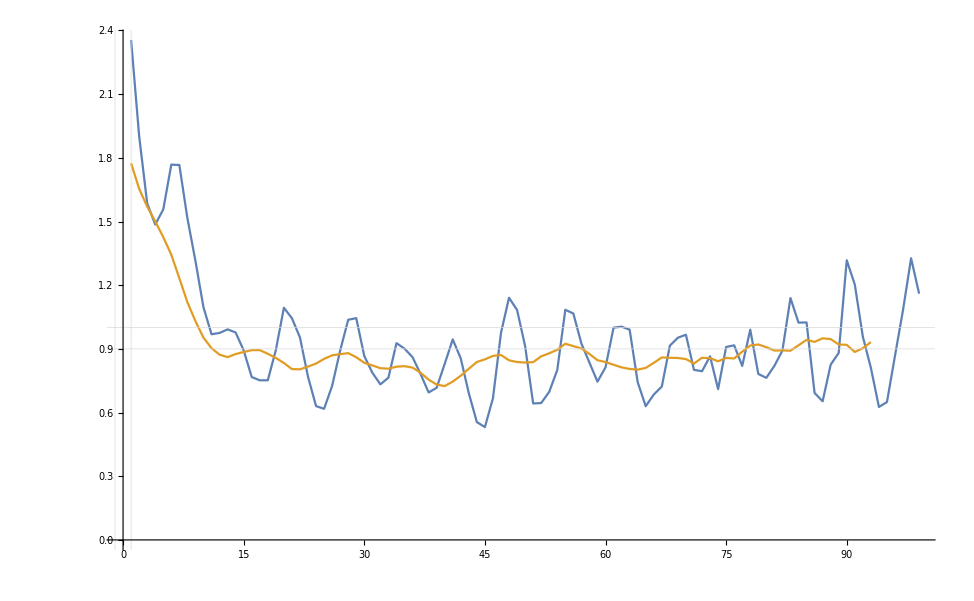

```mathematica
ListPlot[{a,MovingAverage[a,7]},PlotRange->All,Joined->True,GridLines->{{-1,0,1}, {-1,0,0.9,1}},GridLinesStyle->{{},{1->Red}}]
```

```mathematica
ToNormal[g_]:=Block[{edges=EdgeList[g]},
Table[edges=(edges/. VertexList[g][[k]]->k),{k,VertexCount[g]}];
Graph[Range[VertexCount[g]],edges]
]
```

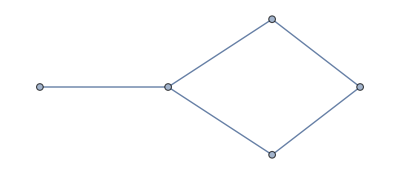

```mathematica
UndirectedGraph[FormulaGraphReverse2[FindFullFormula[ReadGrof[3]]]]//ToNormal
```

```mathematica
DoIt[g_,n_]:=Block[{i,current=g, result={}},
AppendTo[result,Labeled[Graph[current,VertexLabels->"Name"],PlanarGraphQ[current]]];
For[i=1,i<n,i++,
current=ToNormal[UndirectedGraph[FormulaGraphReverse2[FindFullFormula[current]]]];
AppendTo[result,Labeled[Graph[current,VertexLabels->"Name"],PlanarGraphQ[current]]];
If[VertexCount[current]>10,i=n];
];
result
]
```

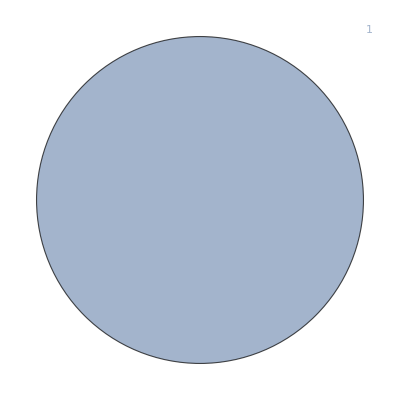
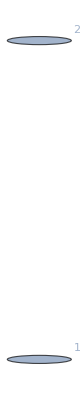
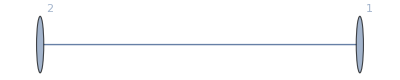
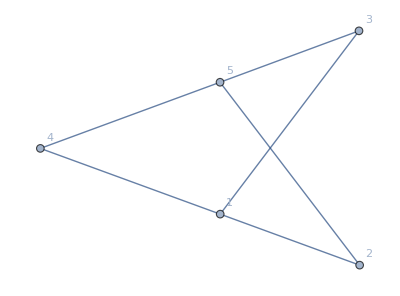
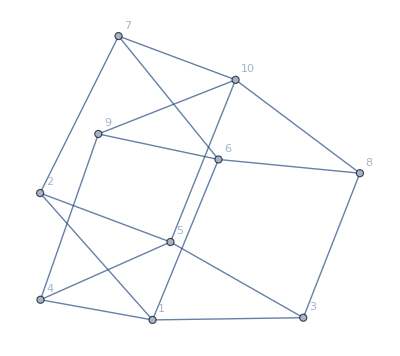
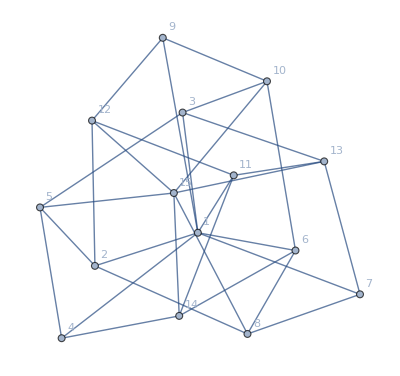
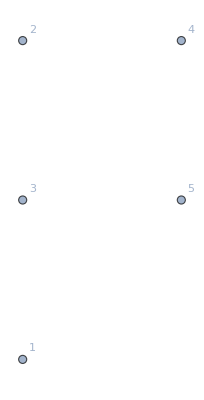
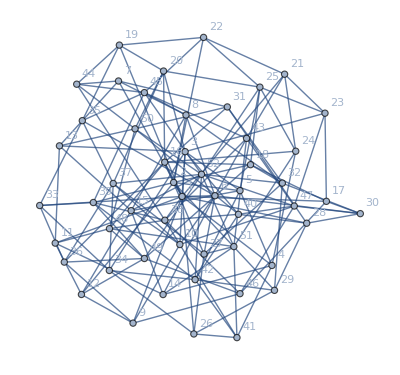
-Graphics-True | -Graphics-True | -Graphics-True
-Graphics-True | -Graphics-True | -Graphics-True
-Graphics-True | -Graphics-True | -Graphics-False
-Graphics-True | -Graphics-False | 
-Graphics-True | -Graphics-False | 
-Graphics-True | -Graphics-False |

```mathematica
Table[DoIt[Graph[Range[k],{}],3],{k,6}]//TableForm
```

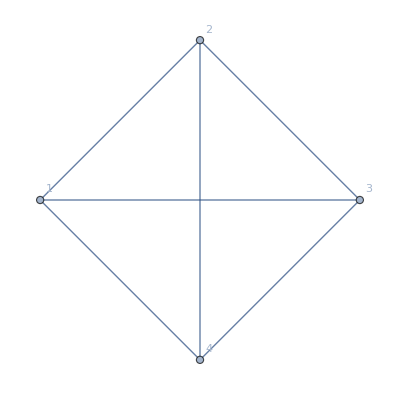
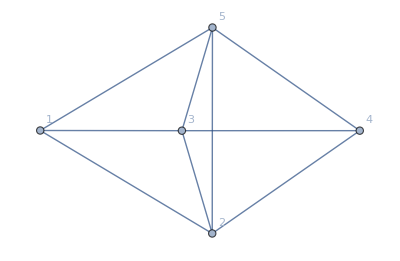
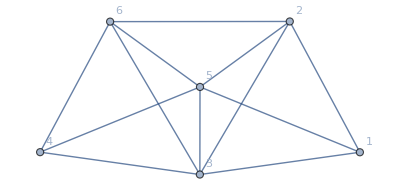
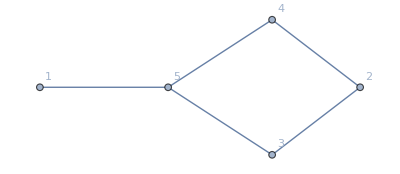
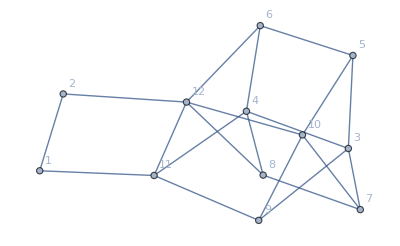
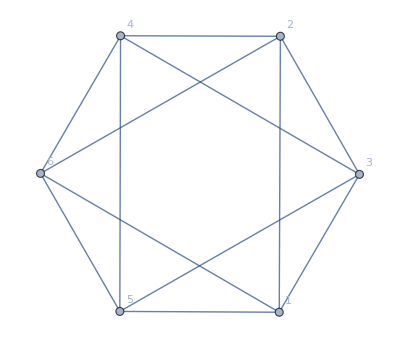
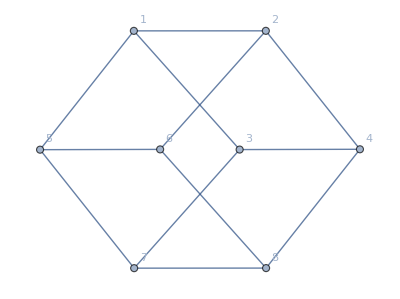
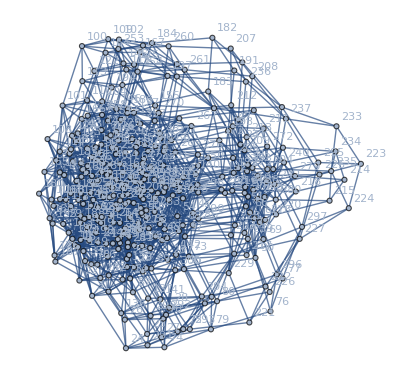
-Graphics-True | -Graphics-True | -Graphics-True
-Graphics-True | -Graphics-True | -Graphics-True
-Graphics-True | -Graphics-True | -Graphics-False
-Graphics-True | -Graphics-True | -Graphics-False
-Graphics-True | -Graphics-True | 
-Graphics-True | -Graphics-True | 
-Graphics-True | -Graphics-False | 
-Graphics-True | -Graphics-False | 
-Graphics-True | -Graphics-False | 
-Graphics-True | -Graphics-False | 
-Graphics-True | -Graphics-False | 
-Graphics-True | -Graphics-False | 
-Graphics-True | -Graphics-False | 
-Graphics-True | -Graphics-False | 
-Graphics-True | -Graphics-False | 
-Graphics-True | -Graphics-False | 
-Graphics-True | -Graphics-False | 
-Graphics-True | -Graphics-False | 
-Graphics-True | -Graphics-False | 
-Graphics-True | -Graphics-False |

```mathematica
Table[DoIt[ReadGrof[k],3],{k,20}]//TableForm
```

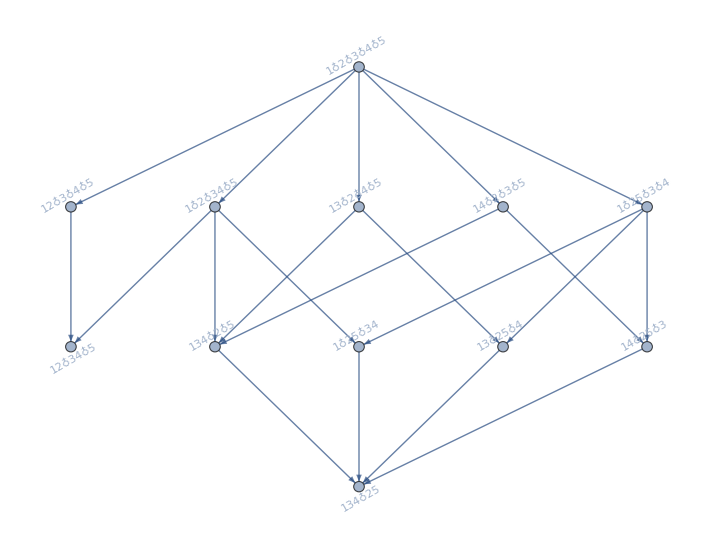

```mathematica
FindFullFormula[-Graphics-]//FormulaGraphReverse2
```

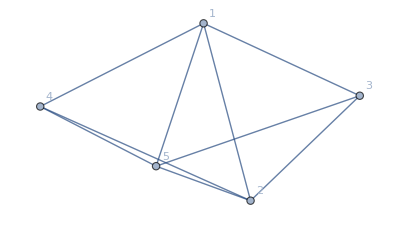
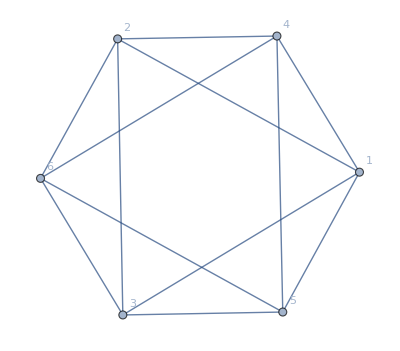
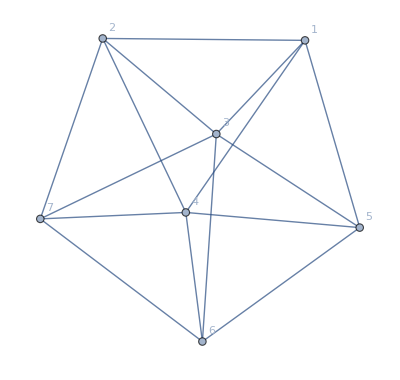
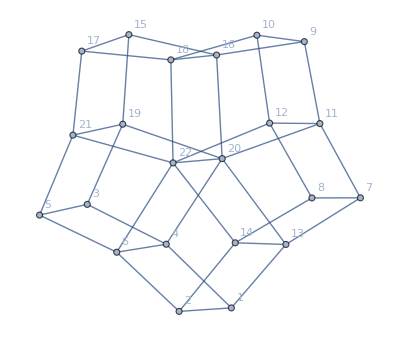
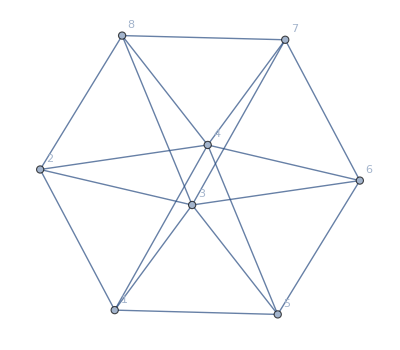
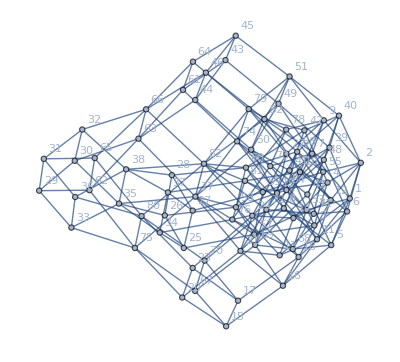
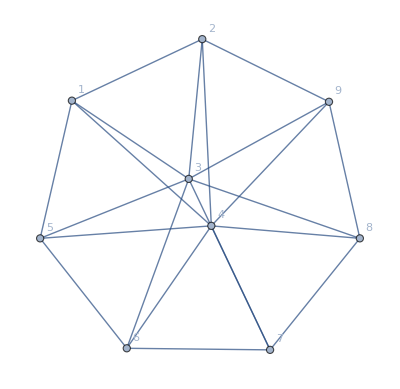
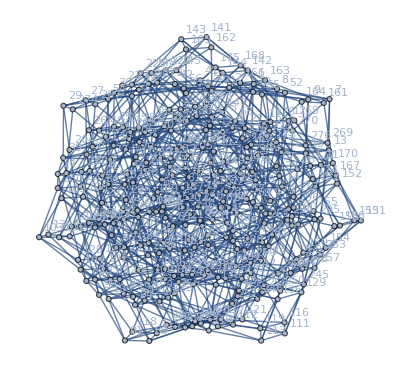
-Graphics-True | -Graphics-True | -Graphics-True
-Graphics-True | -Graphics-True | -Graphics-False
-Graphics-True | -Graphics-False | 
-Graphics-True | -Graphics-False | 
-Graphics-True | -Graphics-False | 
-Graphics-True | -Graphics-False |

```mathematica
Table[DoIt[JacobsThalGraph[k],3],{k,6}]//TableForm
```

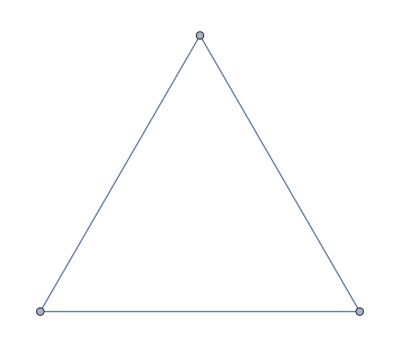

```mathematica
CycleGraph[3]
```

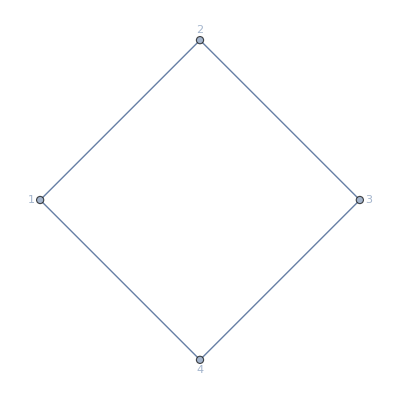
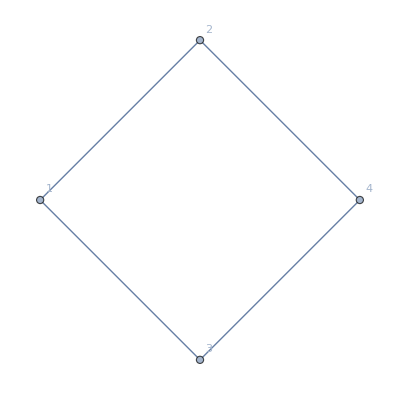
{-Graphics-True,-Graphics-True,-Graphics-True}

```mathematica
DoIt[CycleGraph[4],3]
```

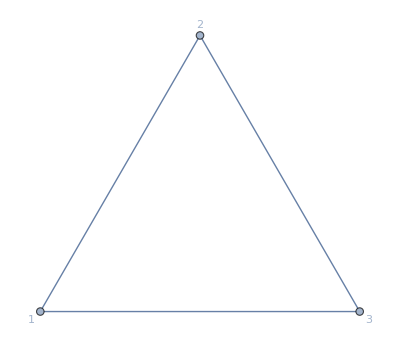
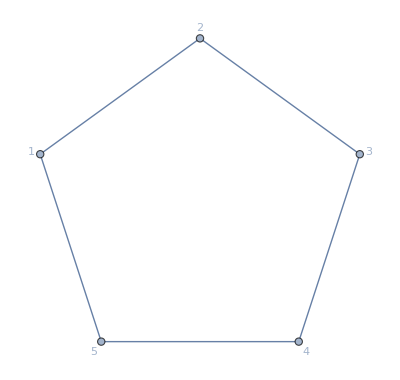
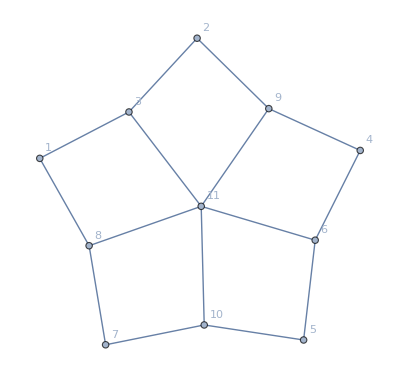
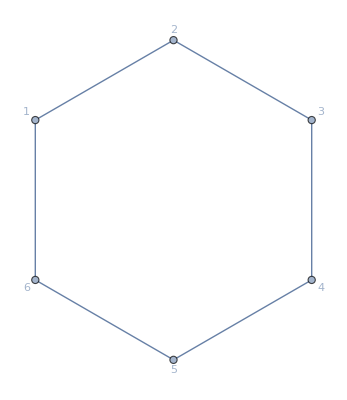
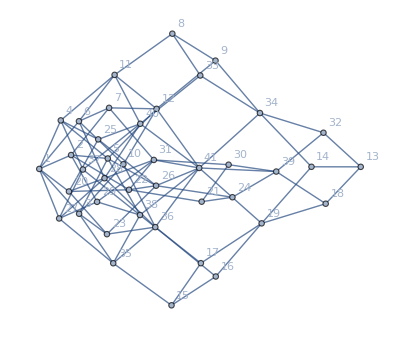
-Graphics-True | -Graphics-True | -Graphics-True
-Graphics-True | -Graphics-True | -Graphics-True
-Graphics-True | -Graphics-True | 
-Graphics-True | -Graphics-False |

```mathematica
Table[DoIt[CycleGraph[k],3],{k,3,6}]//TableForm
```